## General CF algorithm

### Performance on SBCL

```mathematica
runtimes[sbcl]={{10, 0.004}, {20, 0.045}, {30, 0.45}, {40, 2.46}, {50, 9.249}, {60, 26.75}, {70, 90.57}, {80, 232.46}, {90, 527.5}}
```

{{10,0.004},{20,0.045},{30,0.45},{40,2.46},{50,9.249},{60,26.75},{70,90.57},{80,232.46},{90,527.5}}

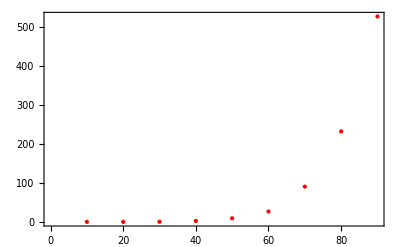

```mathematica
dataplot[sbcl] = ListPlot[runtimes[sbcl], Joined -> False, PlotStyle -> {Red, Thick}, Frame -> True]
```

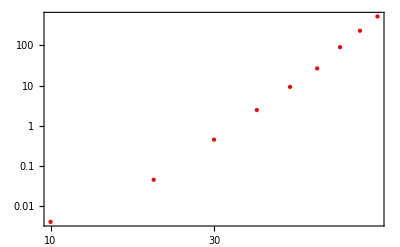

```mathematica
ListLogLogPlot[runtimes[sbcl], Joined -> False, PlotStyle -> Red, Frame -> True]
```

```mathematica
f[t_] := Exp[b t]
params = {b}
```

{b}

```mathematica
fit[sbcl] = FindFit[Take[runtimes[sbcl], 9], f[t], params, t]
```

{b→0.0692023}

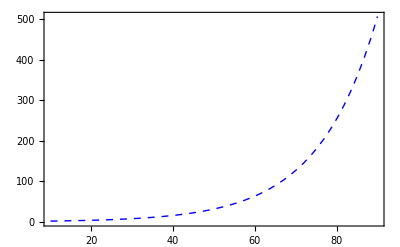

```mathematica
fitplot[sbcl] = Plot[f[t] /. fit[sbcl], {t, 10, 90}, PlotStyle -> {Blue, Dashed}, Frame -> True]
```

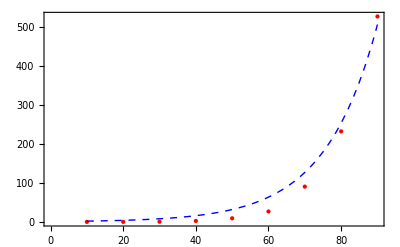

```mathematica
Show[{dataplot[sbcl], fitplot[sbcl]}]
```

```mathematica
<< Units`
```

```mathematica
Convert[
  (f[250] /. fit[sbcl]) Second,
  Day]
```

377.598 Day

```mathematica
Convert[
  (f[100] /. fit[sbcl]) Second,
  Minute]
```

16.8759 Minute

```mathematica
Convert[
  (f[90] /. fit[sbcl]) Second,
  Minute]
```

8.44743 Minute

### Performance on CLISP

```mathematica
runtimes[clisp]={{10, 0.009}, {20, 0.028}, {30, 0.168}, {40, 0.956}, {50, 4.489135}, {60, 17.552}, {70, 60}, {80, 179.3}, {90, 752.7}}
```

{{10,0.009},{20,0.028},{30,0.168},{40,0.956},{50,4.48914},{60,17.552},{70,60},{80,179.3},{90,752.7}}

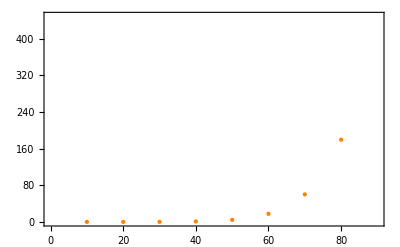

```mathematica
dataplot[clisp]=ListPlot[runtimes[clisp],Joined->False,PlotStyle->{Orange,Thick},Frame->True]
```

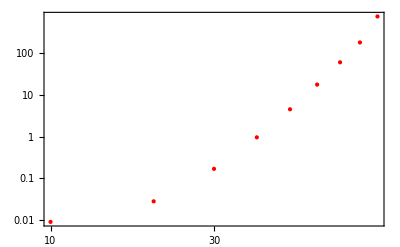

```mathematica
ListLogLogPlot[runtimes[clisp],Joined->False,PlotStyle->Red,Frame->True]
```

```mathematica
f[t_]:=Exp[b t]
params={b}
```

{b}

```mathematica
fit[clisp]=FindFit[Take[runtimes[clisp],9],f[t],params,t]
```

{b→0.0722498}

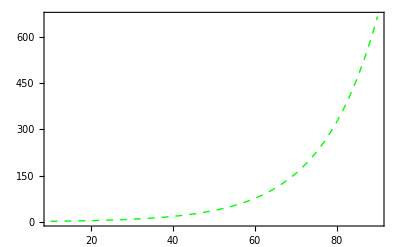

```mathematica
fitplot[clisp]=Plot[f[t]/.fit[clisp],{t,10,90},PlotStyle->{Green,Dashed},Frame->True]
```

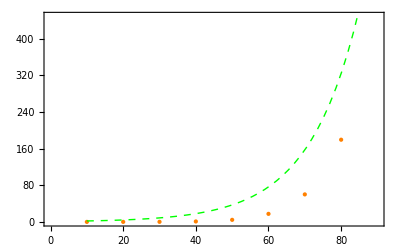

```mathematica
Show[{dataplot[clisp],fitplot[clisp]}]
```

```mathematica
<<Units`
```

```mathematica
Convert[
(f[250]/.fit[clisp]) Second,
Day]
```

808.926 Day

```mathematica
Convert[
(f[100]/.fit[clisp]) Second,
Minute]
```

9.46021 Minute

```mathematica
Convert[
(f[90]/.fit[clisp]) Second,
Minute]
```

11.1132 Minute

### Comparison

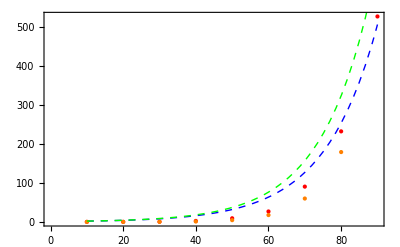

```mathematica
Show[{dataplot[sbcl],fitplot[sbcl],dataplot[clisp],fitplot[clisp]}]
```